# Chapter 3

## Example 3.1

```mathematica
Remove["Global`*"]
A={1,3,-1};
Print["The normalized vector is",A/Norm[A]]
```

Remove::rmnsm: There are no symbols matching "Global`*".

The normalized vector is{1/(√11),3/(√11),-1/(√11)}

## Example 3.4

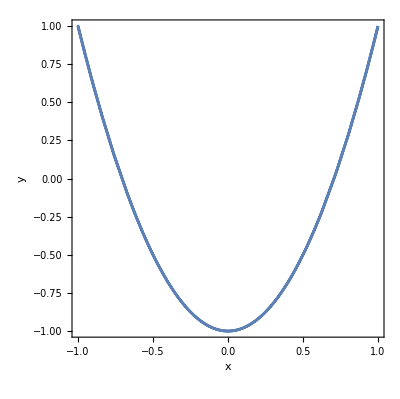

```mathematica
Remove["Global`*"]
SetOptions[ParametricPlot,BaseStyle->FontSize->16, Frame->True];ParametricPlot[{Cos[t],Cos[2*t]},{t,0,2*Pi},AxesLabel->{x,y}]
```

## Example 3.5

```mathematica
Remove["Global`*"]
SetOptions[ParametricPlot3D,BaseStyle->FontSize->20];ParametricPlot3D[{1+2*Cos[2*t],2+4*Sin[2*t],t},{t,0,4},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Example 3.6

```mathematica
Remove["Global`*"]
A={3,4,-1};
B= {1,-1,-1};
Print["The dot product of A.B = ",Dot[A,B]]
```

The dot product of A.B = 0

## Example 3.8

```mathematica
Remove["Global`*"]
A={3,4,-1};
B= {1,-1,-1};
Print["The cross product of A.B = ",Cross[A,B]]
```

The cross product of A.B = {-5,2,-7}

## Example 3.9

```mathematica
Remove["Global`*"]
A={1,3,-1};
B= {4,-2,1};
c =Cross[A,B];
Print["The cross product of A.B = ",c]
Print["The normalized vector is",c/Norm[c]]
```

The cross product of A.B = {1,-5,-14}

The normalized vector is{1/(√222),-5/(√222),-7 √(2/111)}

## Example 3.10

```mathematica
Remove["Global`*"]
a={ax,ay,az};
b= {bx,by,bz};
c ={cx,cy,cz};
Print["The triple product of a.(bxc) = "]
Print[Dot[a,Cross[b,c]]]
```

The triple product of a.(bxc) =

az (-by cx+bx cy)+ay (bz cx-bx cz)+ax (-bz cy+by cz)

```mathematica
check=(Dot[a,Cross[b,c]]==Dot[b,Cross[c,a]]//Simplify);
Print["The identity a.(bxc)= b.(cxa) is: ",check]
```

The identity a.(bxc)= b.(cxa) is: True

## Example 3.11

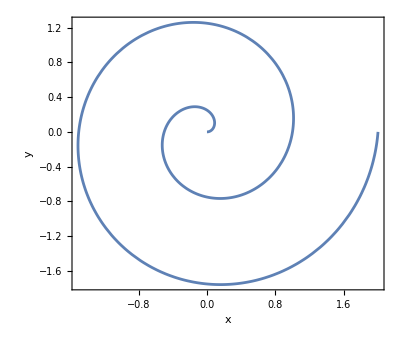

```mathematica
Remove["Global`*"]
SetOptions[PolarPlot,BaseStyle->FontSize->16, Frame->True];
PolarPlot[θ/(2*Pi),{θ,0,4*Pi},AxesLabel->{x,y}]
```

## Example 3.12a

{{r→-1/(√(1/b^2+Cos[θ]^2/a^2-Cos[θ]^2/b^2))},{r→1/(√(1/b^2+Cos[θ]^2/a^2-Cos[θ]^2/b^2))}}

1/(√(1/b^2+Cos[θ]^2/a^2-Cos[θ]^2/b^2))

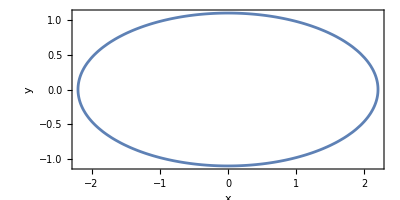

```mathematica
Remove["Global`*"]
SetOptions[PolarPlot,BaseStyle->FontSize->16];
x=r*Cos[θ];
y=r*Sqrt[1-Cos[θ]^2];
sol=Solve[(x/a)^2+(y/b)^2==1,r]

rellipse=r/.sol[[2]]
PolarPlot[rellipse/.{a->2.2,b->1.1},{θ,0,2*Pi},AxesLabel->{"x","y"}]
```

## Example 3.12b

```mathematica
Remove["Global`*"]
SetOptions[PolarPlot,BaseStyle->FontSize->16];

c=Sqrt[a^2-b^2];
x=r*Cos[θ];y=r*Sqrt[(1-Cos[θ]^2)];
sol2=Solve[((x+c)/a)^2+(y/b)^2==1,r]//FullSimplify;

rellipse2=r/.sol2[[1]]//FullSimplify;
Print["The equation of the new ellipse is:"]
Print[rellipse2]
```

The equation of the new ellipse is:

b^2/(a+√((a-b) (a+b)) Cos[θ])

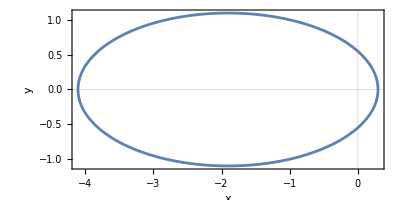

```mathematica
PolarPlot[rellipse2/.{a->2.2,b->1.1},{θ,0,2*Pi},GridLines->{{0},{0}},AxesLabel->{"x","y"}]
```

## Example 3.13

{-2 ⅇ^(-x^2-y^2) x,-2 ⅇ^(-x^2-y^2) y}

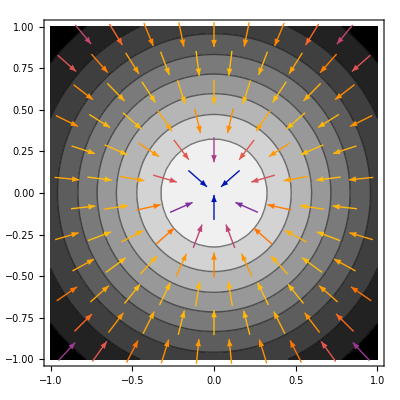

```mathematica
Remove["Global`*"]
SetOptions[ContourPlot,BaseStyle->FontSize->16];

f=Exp[-(x^2+y^2)];
gradf=Grad[f,{x,y}]

gr1=ContourPlot[f,{x,-1,1},{y,-1,1},ColorFunction->GrayLevel];
gr2=VectorPlot[gradf,{x,-1,1},{y,-1,1},VectorStyle->Red,VectorPoints->10];
Show[gr1,gr2]
```

## Example 3.14

```mathematica
Remove["Global`*"]
a={2,-2,1};
n=a/Norm[a];
Print["The normalized vector a is :",n]
Print[]

dirderiv=ResourceFunction["DirectionalD"][x^2*y+x*z,n,{x,y,z}];
Print["The directional derivative function is :"]
Print[dirderiv]
Print[]

result=dirderiv/.{x->1,y->2,z->-1};
Print["The directional derivative at point(1,2,-1) is : ",result]
```

The normalized vector a is :{2/3,-2/3,1/3}

The directional derivative function is :

x/3-(2 x^2)/3+2/3 (2 x y+z)

The directional derivative at point(1,2,-1) is : 5/3

## Example 3.15

```mathematica
Remove["Global`*"]

f[rho,theta,z]=rho*Sin[theta]*Cos[z];

Print["The gradient of the  f in cylidrical coordinates is:"];
Grad[f[rho,theta,z],{rho,theta,z},"Cylindrical"]
```

The gradient of the  f in cylidrical coordinates is:

{Cos[z] Sin[theta],Cos[theta] Cos[z],-rho Sin[theta] Sin[z]}

## Example 3.16

```mathematica
Remove["Global`*"]

LHS=Grad[f[x_,y_,z_]*g[x_,y_,z_],{x,y,z}];
RHS=Grad[f[x_,y_,z_],{x,y,z}]*g[x_,y_,z_]+Grad[g[x_,y_,z_],{x,y,z}]*f[x_,y_,z_];

Print["The identity is :", LHS==RHS]
```

The identity is :True

## Example 3.17

```mathematica
Remove["Global`*"]

v={x*y*z,x*y*z,x*y*z};
Print["The divergence of the vector field is:  ",Div[v,{x,y,z}]]
```

The divergence of the vector field is:  x y+x z+y z

## Example 3.18

```mathematica
Remove["Global`*"]

v={y^2*z,x*z,x*y};
curlv=Curl[v,{x,y,z}];
Print["The curl of the vector field is:  ",curlv]
```

The curl of the vector field is:  {0,-y+y^2,z-2 y z}